## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="GAPD";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_GAPD_typeI";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi; [nad,g3p,pi,13dpg,nadh]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null;nad,Null;pi,Null | 0.452 | 0.4294
0.4746 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad | 0.000045 | 0.000041
0.000049 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 | 
1 | g3p | 0.00089 | 0.00072
0.00106 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22 | teoa | 0.04 | 
1 | pi | 0.00053 | 0.00042
0.00064 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 268 | 262.
274. | 1/s | 8.9 | 22 | teoa | 0.04 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kd | nad | 3.2×10^-7 | 2.5×10^-7
3.9×10^-7 |  | M | 8.9 | 22 | teoa | 0.04 |

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,0.7,1};
s05Priorities = Null;
kcatPriorities = {1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = {1};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi; [nad,g3p,pi,13dpg,nadh]

Structure: 4

Active sites: 4

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p,Null;nad,Null;pi,Null | 0.452 | 0.4294
0.4746 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | nad | 0.000045 | 0.000041
0.000049 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 | 
0.7 | g3p | 0.00089 | 0.00072
0.00106 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22 | teoa | 0.04 | 
1 | pi | 0.00053 | 0.00042
0.00064 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g3p | Null
nad | Null
pi | Null | 268 | 262.
274. | 1/s | 8.9 | 22 | teoa | 0.04 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kd | nad | 3.2×10^-7 | 2.5×10^-7
3.9×10^-7 |  | M | 8.9 | 22 | teoa | 0.04 |

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

```mathematica
catalyticBranch={"E_GAPD[c] + nad[c] <=> E_GAPD[c]&nad",
				"E_GAPD[c]&nad + g3p[c] <=> E_GAPD[c]&nad&g3p",
				"E_GAPD[c]&nad&g3p + pi[c] <=> E_GAPD[c]&nad&g3p&pi",
				"E_GAPD[c]&nad&g3p&pi <=> E_GAPD[c]&nadh&13dpg",
				"E_GAPD[c]&nadh&13dpg <=> E_GAPD[c]&nadh + 13dpg[c]",
				"E_GAPD[c]&nadh<=> E_GAPD[c] + nadh[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,((GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c)^GAPD2,((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,((GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c)^GAPD4,((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((GAPD^c)_^+nad^c⇌(GAPD^c&nad^c)_^)^GAPD1,Overscript[(GAPD^c&nadh^c)_^⇌(GAPD^c)_^+nadh^c, GAPD2],((GAPD^c&nad^c)_^+g3p^c⇌(GAPD^c&nad^c&g3p^c)_^)^GAPD3,Overscript[(GAPD^c&nadh^c&(13dpg)^c)_^⇌(GAPD^c&nadh^c)_^+(13dpg)^c, GAPD4],((GAPD^c&nad^c&g3p^c)_^+pi^c⇌(GAPD^c&nad^c&g3p^c&pi^c)_^)^GAPD5,((GAPD^c&nad^c&g3p^c&pi^c)_^⇌(GAPD^c&nadh^c&(13dpg)^c)_^)^GAPD6};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

### Build enzyme model

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};


inhibitionListSubset=inhibitionList;
customRatiosDataList={{1, (Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶Subscript[k, GAPD5]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵Subscript[k, GAPD5]^⟵), 4.25*10^2,{0.9*4.25*10^2,1.1*4.25*10^2}}};

numTrials=5;
simulateDataFlag="normal";
 nSamples=Null;
paramScanList=Null;
```

```mathematica
{fittingData, filteredDataList, bestFitDetails,
{enzymeModelLocal, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub,
	allCatalyticReactions,nonCatalyticReactions, absoluteFlux, absoluteRateForward,
absoluteRateReverse, relativeRateForward, relativeRateReverse, 
	otherAbsoluteRatesForward, otherAbsoluteRatesReverse}}=
buildFullEnzymeModel[enzymeModel, rxn, pathMASSef, inputPath, outputPath, dataFileName, inhibitionList,inhibitionList, KeqList, kmList, 
					s05List, kcatList, inhibitionList, activationList, otherParmsList,inhibitionListSubset,bufferInfo, ionCharge,
					catalyticReactionsSetsList, otherMetsReverseZeroSub,  otherMetsForwardZeroSub,   customRatiosDataList, MWCFlag,
					simplifyFlag, simplifyMaxTime, nActiveSites, fitLabel, numTrials, simulateDataFlag, nSamples, paramScanList];
```

{g3p^c→0,nad^c→0,pi^c→0}

{(13dpg)^c→0,nadh^c→0}

{g3p^c→∞,nad^c→∞,pi^c→∞}

{(13dpg)^c→∞,nadh^c→∞}

{}

{((GAPD^c&nad^c&g3p^c&pi^c)_^-((GAPD^c&nadh^c&(13dpg)^c)_^)/K_GAPD6) Volume_c k_GAPD6^⟶}

Loading flux equation...

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate forward equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Loading relative rate reverse equation...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Configuring enzyme fits...

Running enzyme fit...

Evaluating fitness results...

ENd

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.000538033 | 2.8948×10^-7 | 0.000560315 | 0.123963 | 0.452 | 0.45256
1 | haldaneRatio_1 | 0.000538033 | 2.8948×10^-7 | 0.000560315 | 0.123963 | 0.452 | 0.45256
1 | haldaneRatio_1 | 0.000538033 | 2.8948×10^-7 | 0.000560315 | 0.123963 | 0.452 | 0.45256
1 | haldaneRatio_1 | 0.000538033 | 2.8948×10^-7 | 0.000560315 | 0.123963 | 0.452 | 0.45256
1 | haldaneRatio_1 | 0.000538033 | 2.8948×10^-7 | 0.000560315 | 0.123963 | 0.452 | 0.45256
1 | haldaneRatio_1 | 0.000538033 | 2.8948×10^-7 | 0.000560315 | 0.123963 | 0.452 | 0.45256
1 | haldaneRatio_1 | 0.000538033 | 2.8948×10^-7 | 0.000560315 | 0.123963 | 0.452 | 0.45256
1 | haldaneRatio_1 | 0.000538033 | 2.8948×10^-7 | 0.000560315 | 0.123963 | 0.452 | 0.45256
1 | haldaneRatio_1 | 0.000538033 | 2.8948×10^-7 | 0.000560315 | 0.123963 | 0.452 | 0.45256
1 | haldaneRatio_1 | 0.000538033 | 2.8948×10^-7 | 0.000560315 | 0.123963 | 0.452 | 0.45256
1 | haldaneRatio_1 | 0.000538033 | 2.8948×10^-7 | 0.000560315 | 0.123963 | 0.452 | 0.45256
1 | relRateFor_nad | 0.00784566 | 0.0000615544 | 0.00162755 | 1.79031 | 0.0909091 | 0.0892815
1 | relRateFor_nad | 0.00745293 | 0.0000555462 | 0.00232771 | 1.70146 | 0.136807 | 0.134479
1 | relRateFor_nad | 0.00690512 | 0.0000476806 | 0.00316677 | 1.57739 | 0.20076 | 0.197593
1 | relRateFor_nad | 0.00618464 | 0.0000382498 | 0.00402625 | 1.41397 | 0.284747 | 0.280721
1 | relRateFor_nad | 0.00530704 | 0.0000281646 | 0.00469866 | 1.21455 | 0.386863 | 0.382165
1 | relRateFor_nad | 0.00433264 | 0.0000187718 | 0.00496334 | 0.992668 | 0.5 | 0.495037
1 | relRateFor_nad | 0.00335606 | 0.0000112631 | 0.00471982 | 0.769782 | 0.613137 | 0.608417
1 | relRateFor_nad | 0.00247271 | 6.1143×10^-6 | 0.00406081 | 0.567745 | 0.715253 | 0.711192
1 | relRateFor_nad | 0.00174484 | 3.04446×10^-6 | 0.00320462 | 0.400958 | 0.79924 | 0.796035
1 | relRateFor_nad | 0.00118977 | 1.41556×10^-6 | 0.00236153 | 0.27358 | 0.863193 | 0.860832
1 | relRateFor_nad | 0.000790975 | 6.25641×10^-7 | 0.00165421 | 0.181963 | 0.909091 | 0.907437
0.7 | relRateFor_g3p | 0.0267857 | 0.000717475 | 0.00543754 | 5.98129 | 0.0909091 | 0.0854716
0.7 | relRateFor_g3p | 0.0254723 | 0.000648836 | 0.00779322 | 5.69651 | 0.136807 | 0.129014
0.7 | relRateFor_g3p | 0.0236354 | 0.000558634 | 0.0106339 | 5.29682 | 0.20076 | 0.190126
0.7 | relRateFor_g3p | 0.0212114 | 0.000449922 | 0.0135732 | 4.76674 | 0.284747 | 0.271174
0.7 | relRateFor_g3p | 0.0182457 | 0.000332905 | 0.0159163 | 4.1142 | 0.386863 | 0.370947
0.7 | relRateFor_g3p | 0.0149361 | 0.000223088 | 0.0169035 | 3.38071 | 0.5 | 0.483096
0.7 | relRateFor_g3p | 0.0116012 | 0.000134587 | 0.0161617 | 2.6359 | 0.613137 | 0.596975
0.7 | relRateFor_g3p | 0.00856891 | 0.0000734263 | 0.0139741 | 1.95373 | 0.715253 | 0.701279
0.7 | relRateFor_g3p | 0.00605901 | 0.0000367117 | 0.0110731 | 1.38545 | 0.79924 | 0.788167
0.7 | relRateFor_g3p | 0.00413804 | 0.0000171234 | 0.00818562 | 0.948295 | 0.863193 | 0.855007
0.7 | relRateFor_g3p | 0.00275415 | 7.58533×10^-6 | 0.0057469 | 0.632159 | 0.909091 | 0.903344
1 | relRateFor_pi | 0.0030062 | 9.03722×10^-6 | 0.000631458 | 0.694604 | 0.0909091 | 0.0915405
1 | relRateFor_pi | 0.00285392 | 8.14487×10^-6 | 0.000901973 | 0.659304 | 0.136807 | 0.137709
1 | relRateFor_pi | 0.00264183 | 6.97928×10^-6 | 0.00122495 | 0.610158 | 0.20076 | 0.201985
1 | relRateFor_pi | 0.00236346 | 5.58595×10^-6 | 0.00155384 | 0.545691 | 0.284747 | 0.286301
1 | relRateFor_pi | 0.00202524 | 4.10162×10^-6 | 0.00180827 | 0.467419 | 0.386863 | 0.388671
1 | relRateFor_pi | 0.00165083 | 2.72525×10^-6 | 0.00190421 | 0.380842 | 0.5 | 0.501904
1 | relRateFor_pi | 0.00127674 | 1.63007×10^-6 | 0.00180516 | 0.294414 | 0.613137 | 0.614942
1 | relRateFor_pi | 0.000939371 | 8.82417×10^-7 | 0.00154875 | 0.216532 | 0.715253 | 0.716802
1 | relRateFor_pi | 0.000662089 | 4.38361×10^-7 | 0.00121938 | 0.152568 | 0.79924 | 0.800459
1 | relRateFor_pi | 0.000451067 | 2.03462×10^-7 | 0.000896996 | 0.103916 | 0.863193 | 0.86409
1 | relRateFor_pi | 0.000299685 | 8.98111×10^-8 | 0.000627535 | 0.0690288 | 0.909091 | 0.909718
1 | absRateFor | 9.12779×10^-7 | 8.33165×10^-13 | 0.000563269 | 0.000210175 | 268 | 267.999
1 | absRateFor | 9.12779×10^-7 | 8.33165×10^-13 | 0.000563269 | 0.000210175 | 268 | 267.999
1 | absRateFor | 9.12779×10^-7 | 8.33165×10^-13 | 0.000563269 | 0.000210175 | 268 | 267.999
1 | absRateFor | 9.12779×10^-7 | 8.33165×10^-13 | 0.000563269 | 0.000210175 | 268 | 267.999
1 | absRateFor | 9.12779×10^-7 | 8.33165×10^-13 | 0.000563269 | 0.000210175 | 268 | 267.999
1 | absRateFor | 9.12779×10^-7 | 8.33165×10^-13 | 0.000563269 | 0.000210175 | 268 | 267.999
1 | absRateFor | 9.12779×10^-7 | 8.33165×10^-13 | 0.000563269 | 0.000210175 | 268 | 267.999
1 | absRateFor | 9.12779×10^-7 | 8.33165×10^-13 | 0.000563269 | 0.000210175 | 268 | 267.999
1 | absRateFor | 9.12779×10^-7 | 8.33165×10^-13 | 0.000563269 | 0.000210175 | 268 | 267.999
1 | absRateFor | 9.12779×10^-7 | 8.33165×10^-13 | 0.000563269 | 0.000210175 | 268 | 267.999
1 | absRateFor | 9.12779×10^-7 | 8.33165×10^-13 | 0.000563269 | 0.000210175 | 268 | 267.999
1 | KdRatio_nad | 0.205491 | 0.0422268 | 1.93619×10^-7 | 60.5061 | 3.2×10^-7 | 5.13619×10^-7
1 | KdRatio_nad | 0.205491 | 0.0422268 | 1.93619×10^-7 | 60.5061 | 3.2×10^-7 | 5.13619×10^-7
1 | KdRatio_nad | 0.205491 | 0.0422268 | 1.93619×10^-7 | 60.5061 | 3.2×10^-7 | 5.13619×10^-7
1 | KdRatio_nad | 0.205491 | 0.0422268 | 1.93619×10^-7 | 60.5061 | 3.2×10^-7 | 5.13619×10^-7
1 | KdRatio_nad | 0.205491 | 0.0422268 | 1.93619×10^-7 | 60.5061 | 3.2×10^-7 | 5.13619×10^-7
1 | KdRatio_nad | 0.205491 | 0.0422268 | 1.93619×10^-7 | 60.5061 | 3.2×10^-7 | 5.13619×10^-7
1 | KdRatio_nad | 0.205491 | 0.0422268 | 1.93619×10^-7 | 60.5061 | 3.2×10^-7 | 5.13619×10^-7
1 | KdRatio_nad | 0.205491 | 0.0422268 | 1.93619×10^-7 | 60.5061 | 3.2×10^-7 | 5.13619×10^-7
1 | KdRatio_nad | 0.205491 | 0.0422268 | 1.93619×10^-7 | 60.5061 | 3.2×10^-7 | 5.13619×10^-7
1 | KdRatio_nad | 0.205491 | 0.0422268 | 1.93619×10^-7 | 60.5061 | 3.2×10^-7 | 5.13619×10^-7
1 | KdRatio_nad | 0.205491 | 0.0422268 | 1.93619×10^-7 | 60.5061 | 3.2×10^-7 | 5.13619×10^-7
1 | customRatio_1 | 6.08968×10^-6 | 3.70842×10^-11 | 0.00595931 | 0.00140219 | 425. | 424.994
1 | customRatio_1 | 6.08968×10^-6 | 3.70842×10^-11 | 0.00595931 | 0.00140219 | 425. | 424.994
1 | customRatio_1 | 6.08968×10^-6 | 3.70842×10^-11 | 0.00595931 | 0.00140219 | 425. | 424.994
1 | customRatio_1 | 6.08968×10^-6 | 3.70842×10^-11 | 0.00595931 | 0.00140219 | 425. | 424.994
1 | customRatio_1 | 6.08968×10^-6 | 3.70842×10^-11 | 0.00595931 | 0.00140219 | 425. | 424.994
1 | customRatio_1 | 6.08968×10^-6 | 3.70842×10^-11 | 0.00595931 | 0.00140219 | 425. | 424.994
1 | customRatio_1 | 6.08968×10^-6 | 3.70842×10^-11 | 0.00595931 | 0.00140219 | 425. | 424.994
1 | customRatio_1 | 6.08968×10^-6 | 3.70842×10^-11 | 0.00595931 | 0.00140219 | 425. | 424.994
1 | customRatio_1 | 6.08968×10^-6 | 3.70842×10^-11 | 0.00595931 | 0.00140219 | 425. | 424.994
1 | customRatio_1 | 6.08968×10^-6 | 3.70842×10^-11 | 0.00595931 | 0.00140219 | 425. | 424.994
1 | customRatio_1 | 6.08968×10^-6 | 3.70842×10^-11 | 0.00595931 | 0.00140219 | 425. | 424.994

### Simulated Data and Best Fit Data Plot

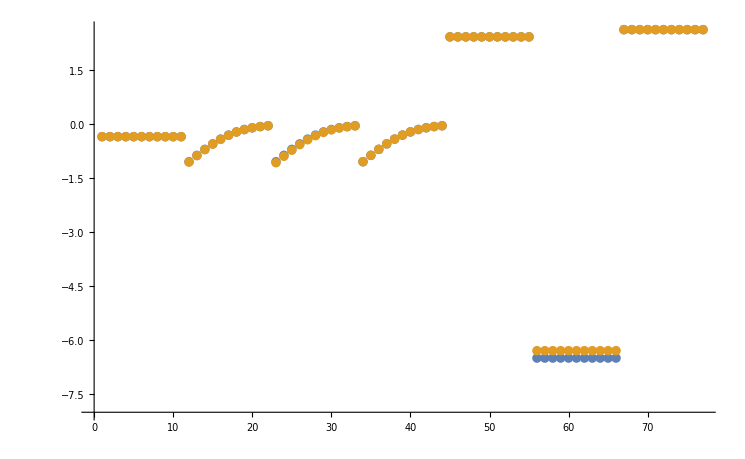

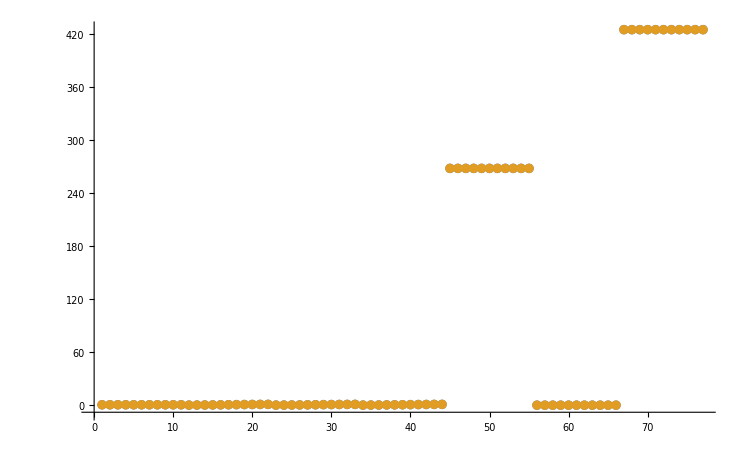

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

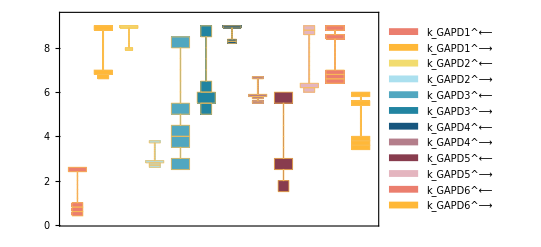

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

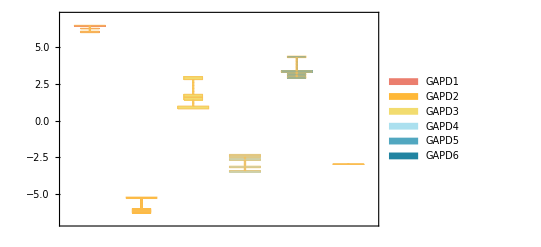

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

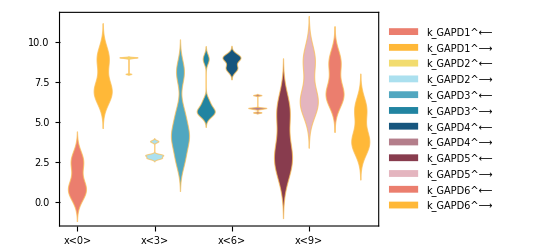

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

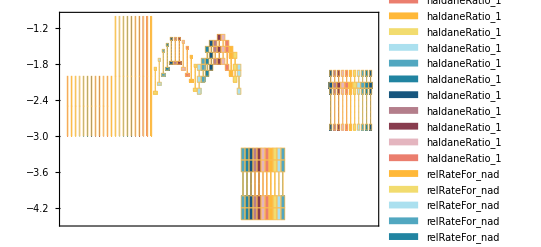

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.0000459024 | 2.00524
0.00089 | 0.000952282 | 6.99799
0.00053 | 0.000525978 | 0.758793

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 267.999 | 0.000210175

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 424.994 | 0.00140219

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.45256 | 0.123963